## Question 1

```mathematica
DSolve[θ''[t]==-θ[t]-3θ'[t],θ[t],t]
```

{{θ[t]→ⅇ^((-3/2-(√5)/2) t) C[1]+ⅇ^((-3/2+(√5)/2) t) C[2]}}

## Question 2

```mathematica
DSolve[{X''[t]==-X[t]-X'[t],X[0]==1,X'[0]==0},X[t],t]
```

{{X[t]→1/3 ⅇ^(-t/2) (3 Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])}}

## Question 3

```mathematica
DSolve[{X'[t]==-X[t]*t,X[0]==1},X[t],t]
```

{{X[t]→ⅇ^(-t^2/2)}}

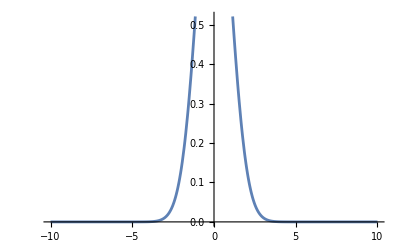

```mathematica
Plot[ⅇ^(-t^2/2),{t,-10,10}]
```

## Question 4

```mathematica
sol=NDSolve[{θ''[τ]==-Sin[θ[τ]]-θ[τ]-Abs[θ'[τ]]*θ'[τ],θ'[0]==1,θ[0]==0.5},θ[τ],{τ,0,10}]
```

{{θ[τ]→InterpolatingFunction[…][τ]}}

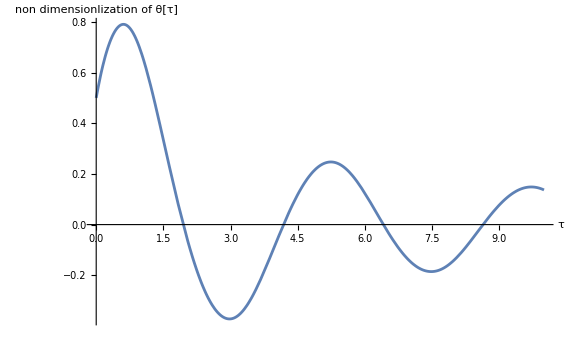

```mathematica
Plot[θ[τ]/.sol,{τ,0,10},AxesLabel->{"τ","non dimensionlization of θ[τ]"},ImageSize->Large]
```